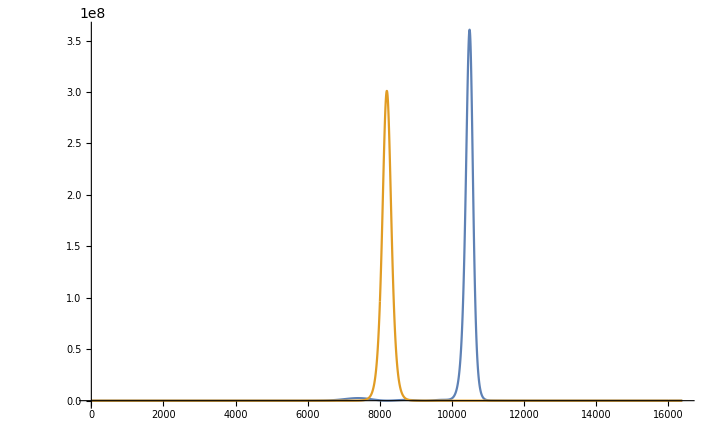

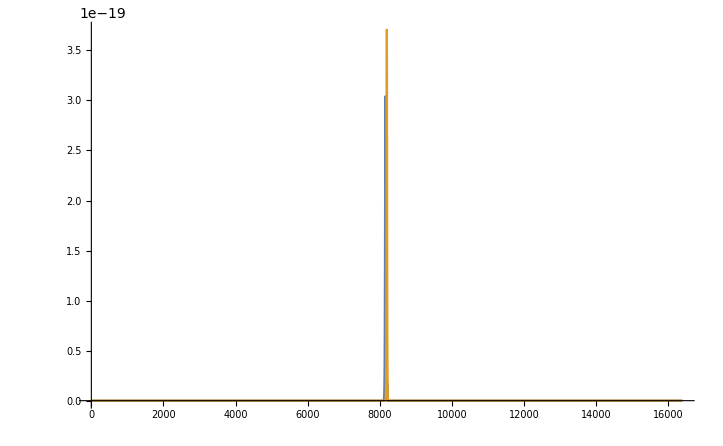

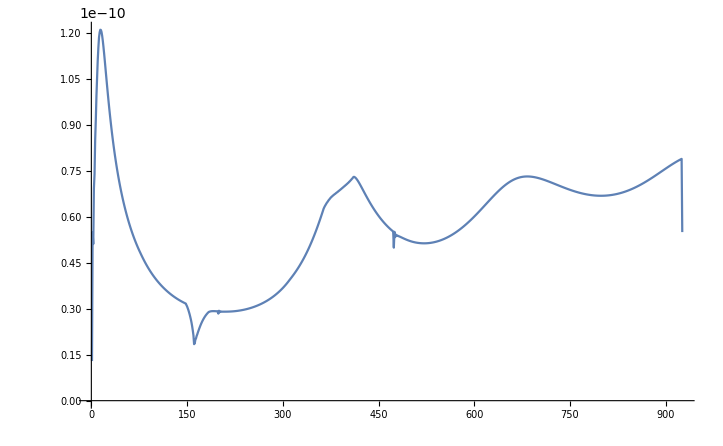

-Graphics3D-

```mathematica
dir = "/home/s_koval/Code/julia/fl";
getCplxData[fname_,dir_]:=Module[{dataRaw},
dataRaw=Import[FileNameJoin[{dir,fname}],"TSV"];
ToExpression[StringReplace[#,{"im"->"*I","e"->"*10^"}]&/@dataRaw]]

u0=Flatten@getCplxData["u0.tsv",dir];
uf=Flatten@getCplxData["uf.tsv",dir];
u0w=Flatten@getCplxData["U0.tsv",dir];
ufw=Flatten@getCplxData["Uf.tsv",dir];
u=Abs/@getCplxData["u_plot.tsv",dir];

steps=Import["/home/s_koval/Code/julia/fl/steps.tsv","TSV"];
s=Flatten[steps];

ListPlot[{Abs[uf]^2, Abs[u0]^2},Joined->True,PlotRange->Full]
ListPlot[{Abs[ufw]^2, Abs[u0w]^2},Joined->True,PlotRange->Full]
ListPlot[s, Joined->True, PlotRange->Full]
ListPlot3D[u, PlotRange->Full]
```

```mathematica
Max[Abs[u0w]]
```

6.08837×10^-10